## Pruebas de geometrías

```mathematica
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; (*Saves nb each 15 minutes*)
StartScheduledTask[saveTask]
```

ScheduledTaskObject[…]

## Paquetes a importar

```mathematica
Needs["MaTeX`"] (*Importa la paquetería de LaTeX*)
SetOptions[MaTeX, "Preamble" -> {"\\usepackage{xcolor}"}]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
(*Directorio donde están las paqueterías*)
SetDirectory["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\Programas\\Packages"]

Needs["MieTheory`"]
```

C:\Users\danal\Documents\Github\Tesis-de-Licenciatura\Programas\Packages

```mathematica
<< "MieTheory.wl"
```

```mathematica
cp=ResourceFunction["CombinePlots"];
```

## Definiciones

```mathematica
h=4.135667696*10^(-15); (*eV s*) (*Constante de Planck*)
hbar=6.582119569*10^(-16); (*eV s*)(*Constante de Planck reducida*)
c=299792458*^9 (*nm s^-1*)(*Velocidad de la luz*);

omega10=Range[0,10,0.01]; 
omegaVis=Range[2,3.1,0.01];
energyTicksMajorVisible={2.07,2.26,2.48,2.76,3.1};

epsPlasma=1.823;


(*Colores*)
blueUNAM=RGBColor[6/255,151/255,213/255];
redUNAM=RGBColor[232/255,68/255,42/255];
gris=RGBColor[127/255,146/255,151/255];
bluelight30=RGBColor[0/255,170/255,212/255];
bluedark30=RGBColor[0/255,51/255,128/255];
bluemedium30=RGBColor[55/255,171/255,200/255];
redlight34=RGBColor[255/255,42/255,42/255];
reddark34=RGBColor[128/255,0/255,0/255];
colorsCHCM={bluelight30,bluedark30,bluemedium30,redlight34,reddark34}
colors2={blueUNAM, redUNAM};
colors={Blue,Red};
color5={Orange};
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x)
rojos=Table[RGBColor[1,g,0],{g,0,0.9,0.16}]
sunsetColors=Table[ColorData["SunsetColors"][i],{i,0,0.8,1/7}]
solarColors=Table[ColorData["SolarColors"][i],{i,0,0.8,1/7}]
alpineColors=Table[ColorData["AlpineColors"][i],{i,0,0.8,1/7}]
lakeColors=Table[ColorData["LakeColors"][i],{i,0,0.8,1/7}]
candyColors=Table[ColorData["CandyColors"][i],{i,0,0.8,1/7}]
verde=RGBColor[150/255,200/255,60/255];
```

{RGBColor[0, Rational[2, 3], Rational[212, 255]],RGBColor[0, Rational[1, 5], Rational[128, 255]],RGBColor[Rational[11, 51], Rational[57, 85], Rational[40, 51]],RGBColor[1, Rational[14, 85], Rational[14, 85]],RGBColor[Rational[128, 255], 0, 0]}

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

{RGBColor[1, 0., 0],RGBColor[1, 0.16, 0],RGBColor[1, 0.32, 0],RGBColor[1, 0.48, 0],RGBColor[1, 0.64, 0],RGBColor[1, 0.8, 0]}

{RGBColor[0., 0., 0.],RGBColor[0.3195368571428571, 0.1164, 0.4341454285714286],RGBColor[0.6695744285714286, 0.22438285714285713, 0.338128],RGBColor[0.8974812857142858, 0.3693308571428571, 0.1452665142857143],RGBColor[0.9882154285714286, 0.5505617142857143, 0.08483494285714285],RGBColor[1., 0.7397017142857143, 0.23300614285714283]}

{RGBColor[0.468742, 0., 0.0158236],RGBColor[0.6706774285714285, 0.06984285714285714, 0.009042057142857144],RGBColor[0.8432481428571429, 0.15849014285714286, 0.008003357142857142],RGBColor[0.9277247142857143, 0.30355071428571423, 0.024193185714285713],RGBColor[0.978545, 0.4534661428571428, 0.0459689],RGBColor[0.995709, 0.6082364285714286, 0.07333049999999999]}

{RGBColor[0.277546, 0.355398, 0.484215],RGBColor[0.3092687142857143, 0.43180485714285716, 0.45451742857142857],RGBColor[0.35382528571428573, 0.4807017142857143, 0.3698534285714286],RGBColor[0.43932542857142853, 0.5335538571428571, 0.38461414285714285],RGBColor[0.5610134285714286, 0.5994675714285714, 0.49026099999999995],RGBColor[0.6995328571428572, 0.6994642857142856, 0.6226554285714285]}

{RGBColor[0.293416, 0.0574044, 0.529412],RGBColor[0.40930385714285716, 0.25890179999999996, 0.6923064285714285],RGBColor[0.5251917142857143, 0.46039919999999995, 0.8552008571428571],RGBColor[0.6206238571428572, 0.6188315714285714, 0.9107938571428571],RGBColor[0.7058281428571428, 0.7557314285714285, 0.9127361428571429],RGBColor[0.7881374285714285, 0.8555037142857143, 0.9026041428571429]}

{RGBColor[0.405188, 0.204349, 0.343389],RGBColor[0.6033010000000001, 0.22473442857142858, 0.36270257142857143],RGBColor[0.7647998571428571, 0.3022755714285714, 0.4413708571428571],RGBColor[0.8306595714285715, 0.45290014285714286, 0.5840857142857143],RGBColor[0.7940618571428572, 0.5946167142857143, 0.7287942857142857],RGBColor[0.7161124285714285, 0.7039788571428571, 0.8368194285714285]}

## Funciones

```mathematica
dataQext[dataCabs_,dataCsca_]:=Module[{dataCext},
dataCext=Transpose[{dataCabs[[All,1]],dataCabs[[All,2]]+dataCsca[[All,2]]}]]

errorAbs[data1_,data2_]:=Module[{error},
error=Abs[data1-data2]]

errorRel[data1_,data2_]:=Module[{error},
error=100*Abs[data1-data2]/data2]
```

## Gráficas

```mathematica
plotStyling = {PlotRange -> All,
   PlotStyle -> (Directive[#, Thickness[0.003]] & /@ colorsCHCM),  
   Frame -> True,
   FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
   LabelStyle->{FontFamily->"Latin Modern Roman 10",Magnification->1.6},
   ImagePadding->{{50,10},{50,50}}};
  
plotPolarStyling = {PlotMarkers->{"●",4.5},
    PlotStyle -> (Directive[#, Thickness[0.002]] & /@ colorsCHCM),
    PlotRange -> 270, 
    Joined->True,
    PolarAxes -> True,
    PolarTicks -> {Drop[Table[i, {i, 0, 2 Pi, Pi/6}], -1], Automatic},
    PolarGridLines -> {Table[a Degree, {a, 0, 360, 30}], {0, 50, 100,150}},
    GridLinesStyle -> Directive[Gray, Dashed],
 
 BaseStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
 ImagePadding->{{50,20},{5,5}}};
  
  
  
  SetDirectory["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\Figuras\\4-Resultados"]
```

C:\Users\danal\Documents\Github\Tesis-de-Licenciatura\Figuras\4-Resultados

## Eritrocito sano

### Propiedades ópticas

#### Importación y preparación de datos

```mathematica
dataEriSanoFF6321=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Sano_Cassini_original.csv"];
dataEriSanoFF6322=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Sano_Cassini_real.csv"];

dataThetaEriSano1=Drop[dataEriSanoFF6321,1][[All,1]];
dataPhiEriSano1=Drop[dataEriSanoFF6321,1][[All,2]];
dataRCSEriSano1=Drop[dataEriSanoFF6321,1][[All,3]];

dataThetaEriSano2=Drop[dataEriSanoFF6322,1][[All,1]];
dataPhiEriSano2=Drop[dataEriSanoFF6322,1][[All,2]];
dataRCSEriSano2=Drop[dataEriSanoFF6322,1][[All,3]];

data6321 = Transpose[{dataThetaEriSano1 *Pi/180, dataPhiEriSano1*Pi/180, dataRCSEriSano1}];
data6321Linear = Transpose[{dataThetaEriSano1 *Pi/180, dataPhiEriSano1*Pi/180, 10^(dataRCSEriSano1/10)}];
fInterp6321 = Interpolation[data6321,InterpolationOrder->1];
fInterp6321Linear = Interpolation[data6321Linear,InterpolationOrder->1];

data6322 = Transpose[{dataThetaEriSano2 *Pi/180, dataPhiEriSano2*Pi/180, dataRCSEriSano2}];
data6322Linear = Transpose[{dataThetaEriSano2 *Pi/180, dataPhiEriSano2*Pi/180, 10^(dataRCSEriSano2/10)}];
fInterp6322 = Interpolation[data6322,InterpolationOrder->1];
fInterp6322Linear = Interpolation[data6322Linear,InterpolationOrder->1];
```

#### lambda = 632.8 nm

```mathematica
dataFF6321DegreeLinear=Table[{th*180/Pi,fInterp6321Linear[th, Pi/2]}, {th, 0,  Pi,  Pi/360}];
dataFF63210DegreeLinear=Table[{th*180/Pi,fInterp6321Linear[th, 0]}, {th, 0,  Pi,  Pi/360}];

dataFF6322DegreeLinear=Table[{th*180/Pi,fInterp6322Linear[th, Pi/2]}, {th, 0,  Pi,  Pi/360}];
dataFF63220DegreeLinear=Table[{th*180/Pi,fInterp6322Linear[th, 0]}, {th, 0,  Pi,  Pi/360}];
```

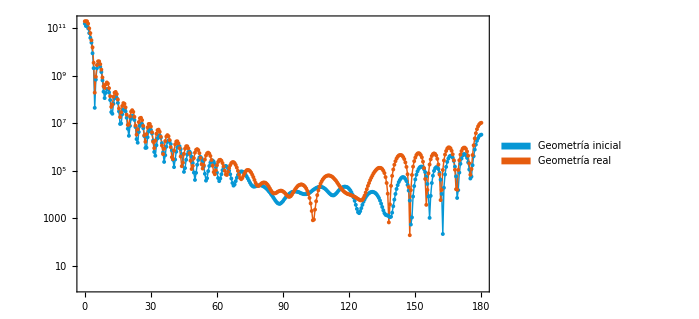

```mathematica
comparacionpaper=ListPlot[{dataFF63210DegreeLinear,dataFF63220DegreeLinear},ScalingFunctions->"Log",
                  PlotMarkers->{"●",4},
                      Joined->True,
                      PlotRange->{{Automatic,Automatic},{1.3,Automatic}},
                      PlotStyle -> {Directive[blueUNAM, Thickness[0.002]],Directive[colors[[1]], Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega "],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                                
                       PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"Geometría inicial","Geometría real"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    Spacings->0.05],{0.5,0.83}],
                      ImagePadding->{{60,10},{60,50}},
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["paperComp.svg",comparacionpaper]
```

paperComp.svg

```mathematica
interv1=Table[{x, x + 5}, {x, 5, 90,5}];
interv2=Table[{x - 5, x + 5}, {x, 105, 174,10}]
intervals=Join[interv1,interv2]
```

{{100,110},{110,120},{120,130},{130,140},{140,150},{150,160},{160,170}}

{{5,10},{10,15},{15,20},{20,25},{25,30},{30,35},{35,40},{40,45},{45,50},{50,55},{55,60},{60,65},{65,70},{70,75},{75,80},{80,85},{85,90},{90,95},{100,110},{110,120},{120,130},{130,140},{140,150},{150,160},{160,170}}

```mathematica
f6321[x_]:=fInterp6321Linear[x*Pi/180,0]/(4 Pi)
 f6322[x_]:=fInterp6322Linear[x*Pi/180,0]/(4 Pi)
 locpaper=GoldenSearchMax[f6321, #1, #2, 0.0005] & @@@ intervals
 locCST=GoldenSearchMax[f6322, #1, #2, 0.0005] & @@@ intervals
 
 Mean[Abs[locpaper-locCST]]
```

{6.49947,13.9999,18.,21.5003,25.5004,33.9994,38.,42.5003,47.4997,52.4997,58.,63.9999,65.0007,71.0001,79.4996,80.0007,85.0007,94.9993,107.,118.,129.999,130.5,144.5,152.999,166.}

{6.49947,13.9999,17.5003,21.5003,29.4996,33.4997,37.5003,42.,46.4995,51.0001,56.0001,61.4995,67.4997,73.9999,75.0007,81.4995,88.9999,90.0007,109.999,111.,120.001,134.,143.499,151.5,165.5}

2.39969

```mathematica
f6320[x_]:=fInterp632LinearTsi[x*Pi/180,0]/(4 Pi)
 locpaper0=GoldenSearchMax[datapaper0, #1, #2, 0.0005] & @@@ intervals
 locCST0=GoldenSearchMax[f6320, #1, #2, 0.0005] & @@@ intervals
 
 Mean[Abs[locpaper0-locCST0]]
```

{5.65115,13.7952,17.618,21.4405,29.4183,33.0748,37.0635,41.2194,46.8699,51.8557,56.5094,62.6587,68.9748,70.0007,75.1249,80.0007,88.7537,90.0007,101.551,112.853,129.999,133.13,141.606,157.563,168.033}

{6.0001,13.9999,17.5003,21.5003,28.9999,33.4997,37.4997,42.,46.4995,51.0001,56.4995,62.,68.4997,70.0007,75.5004,80.0007,89.4996,90.0007,100.5,111.5,125.,133.5,141.499,156.5,167.5}

0.630358